```mathematica
Tau=2Pi;
concentricExact[{r1_,r2_}]:=Block[{
dI=D[BesselI[#1,x],x]/.{x->#2}&,
dK=D[BesselK[#1,x],x]/.{x-> #2}&,
n0=Ceiling[Log[0.01]/(2 Log[r1/r2])]
},
Sum[NIntegrate[Log[1-(dI[k,y r1] dK[k,y r2])/(dI[k, y r2] dK[k,y r1])],{y,0,Infinity}],{k,0,n0}]
];

concentricCoefficients[rs_,ϵ_][w_][n_][α_,β_][i_,j_]:=
Module[{s,x,normal,d},
s[k_]:=(k-1/2)/n;
normal[γ_,k_]:=If[γ==1,1,-1]{Cos[Tau s[k]], Sin[Tau s[k]]};
x[γ_,k_]:=rs[[γ]] {Cos[Tau s[k]], Sin[Tau s[k]]};
d=x[α,i]-(x[β,j]+ϵ normal[β,j]);
w/Tau  BesselK[1, w Norm[d]](normal[β,j] . Normalize[d])//N
];


concentricSource[rs_,ϵ_][w_][n_][α_,β_][i_,j_]:=If[α==β,
0,
Module[{s,x,normal,d,Db},
s[k_]:=(k-1/2)/n;
normal[γ_,k_]:=If[γ==1,1,-1]*{Cos[Tau s[k]], Sin[Tau s[k]]};
x[γ_,k_]:=rs[[γ]] {Cos[Tau s[k]], Sin[Tau s[k]]};
d[k_]:=x[α,k]-x[β,j]-ϵ normal[β,j];

Db=Module[{coefficients,M,v},
coefficients=concentricCoefficients[rs,ϵ][w][n][β,β];
M=0.5IdentityMatrix[n]+Table[coefficients[ii,jj],{ii,1,n},{jj,1,n}];
v=Table[-1/Tau BesselK[0,w Norm[x[β,k]-x[β,j]-ϵ normal[β,j]]],{k,1,n}];
LinearSolve[M,v]
];

-1/Tau BesselK[0,w Norm[d[i]]]
-w rs[[β]]/n Sum[Db[[k]] BesselK[1,w Norm[d[k]]] normal[β,i] . Normalize[d[k]], {k,1,n}]//N
]//Re
];
```

```mathematica
concentricCoefficients[{1,2},0.1][1][15][1,2][1,1]
```

0.11404

```mathematica
Block[{r1=1,r2=2,ϵ=0.01,n=10},
Module[{pts},
pts=Monitor[
Table[Table[concentricSource[{1,2},0.01][1][n][α,β][i,j],{i,1,n},{j,1,n}],{α,1,2},{β,1,2}]//ArrayFlatten//N,
{ProgressIndicator[((β-1)+2(α-1))*n^2+ (i-1)*n+(j-1),{n^2,3n^2}]}
];
ListPlot3D[pts]//Print;
pts
]
]//MatrixForm
```

-Graphics3D-

```mathematica
Module[{r,ϵ,w,n,pts},
r={1,2};ϵ=0.1;w=1;n=60;
pts=Table[Table[concentricCoefficients[r,ϵ][w][n][α,β][i,j],{i,1,n},{j,1,n}],{α,1,2},{β,1,2}]//ArrayFlatten//N;
{ListPlot3D[pts,PlotRange->All],ListPlot3D[pts,PlotRange->{0,All}],ListPlot3D[pts,PlotRange->{All,0}]}//Print;
ListPlot3D[Table[pts[[i,j]],{i,1,n},{j,1,n}],PlotRange->All]//Print;
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

```mathematica
(* UNIT TESTS *)
Module[{testDiagonalCoefficient,testOpposingCoefficient,testCollinearCoefficient},
testDiagonalCoefficient[] := Module[{r1,r2,ϵ,w,n,α,β,i,j,expected,actual},
r1=RandomReal[];r2=1+RandomReal[];
ϵ=RandomReal[{0.01,0.1}];
w=RandomReal[{1,10}];
n=RandomInteger[{10,20}];
α=β=RandomInteger[{1,2}];
i=j=RandomInteger[{1,n}];
expected=-w/Tau BesselK[1,w ϵ];
actual=concentricCoefficients[{r1,r2},ϵ][w][n][α,β][i,j];
AssertEquals[expected,actual]
];
testOpposingCoefficient[]:=Module[{r,ϵ,w,n,α,β,i,j,expected,actual},
r={RandomReal[],1+RandomReal[]};
ϵ=RandomReal[{0.01,0.1}];
w=RandomReal[{1,10}];
n=2*RandomInteger[{5,10}];
α=RandomInteger[{1,2}];
i=RandomInteger[n/2];
expected=If[α==1,-1,1]w/Tau BesselK[1,w(2r[[α]] + If[α==1,ϵ,-ϵ])];
actual=concentricCoefficients[r,ϵ][w][n][α,α][i,i+n/2];
AssertEquals[expected,actual]
];
testCollinearCoefficient[]:=Module[{r1,r2,ϵ,w,n,α,β,i,j,expected,actual},
r1=RandomReal[];r2=1+RandomReal[];
ϵ=RandomReal[{0.01,0.05}];
w=RandomReal[{1,10}];
n=RandomInteger[{10,20}];
α=RandomInteger[{1,2}];β=3-α;
i=RandomInteger[n];
expected=w/Tau BesselK[1,w Abs[r2-r1-ϵ]];
actual=concentricCoefficients[{r1,r2},ϵ][w][n][α,β][i,i];
AssertEquals[expected,actual]
];

UnitTest[testDiagonalCoefficient,100]//Print;
UnitTest[testOpposingCoefficient,100]//Print;
UnitTest[testCollinearCoefficient,100]//Print;
]
```

RGBColor[0, 1, 0]

RGBColor[0, 1, 0]

RGBColor[0, 1, 0]

```mathematica
Db[r_,w_,n_,ϵ_,η_:0.01,verbose_:True][β_,j_]:=Module[{s,normal,x,e,d0, M, v},
s[k_]:=(k-1/2)/n;
normal[k_]:=If[β==1,1,-1] *{Cos[Tau s[k]], Sin[Tau s[k]]}//N;
x[t_]:=r*{Cos[Tau  t], Sin[Tau t]}//N;
v=Table[-1/Tau BesselK[0,w Norm[x[s[i]]-(x[s[j]]+ϵ normal[j])]], {i,1,n}];

e[i_,k_]:=Piecewise[{
{NIntegrate[r normal[i] . (x[t]-x[s[i]]) / Norm[x[t]-x[s[i]]]^2,{t,(k-1)/n,k/n}],i==k},
{NIntegrate[w r BesselK[1,w Norm[x[t]-x[s[i]]]]normal[i] . Normalize[x[t]-x[s[i]]],{t,(k-1)/n, k/n}], Abs[i-k]/n ≤ η}
},
1/n w r BesselK[1,w Norm[x[s[k]]-x[s[i]]]]normal[i] . Normalize[x[s[k]]-x[s[i]]]
]//Re;

M=ParallelTable[e[i,k],{i,1,n},{k,1,n}]+1/2 IdentityMatrix[n];
If[verbose, Print[ListLinePlot[v,PlotRange->All]]; Print[ListPlot3D[M-0.5IdentityMatrix[n],PlotRange->All]]];
LinearSolve[M,v]
];
```

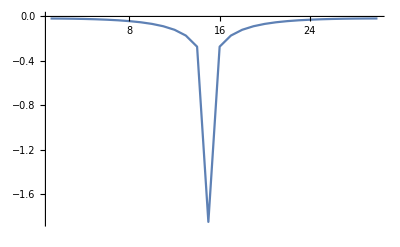

-Graphics3D-

{-0.258889,-0.262807,-0.269497,-0.279213,-0.292341,-0.309438,-0.33129,-0.359021,-0.39428,-0.439594,-0.499141,-0.580645,-0.701279,-0.915503,-4.07937,-0.915503,-0.701279,-0.580645,-0.499141,-0.439594,-0.39428,-0.359021,-0.33129,-0.309438,-0.292341,-0.279213,-0.269497,-0.262807,-0.258889,-0.257598}

```mathematica
Db[1,1,30,0.00001][1,15]
```